```mathematica
frac[δt_, tmaxim_,xint_,yint_,F_,ω_,μ_]:=Module[{funcx,funcy,force,omega,fnext,f,iter,poin,coords,poincoords,traj,proj,strobtraj,poinsec},
funcx[t_,x_ ,y_]:=y;
funcy[t_,x_,y_]:=-μ y+x-x^3+F Cos[ω t];
fnext[x_,y_,t_,h_,f_]:=Module[{k1,k2,k3,k4},
k1=h f[t,x,y];
k2=h f[t +(0.5  h),x +0.5 k1,y+0.5 k1];
k3 =h f[t+(0.5 h),x+0.5 k2,y+0.5 k2];
k4=h f[t+h,x+k3,y+k3];
{ x+1/6 k1+1/3 k2+1/3 k3+1/6 k4,y+1/6 k1+1/3 k2+1/3 k3+1/6 k4}];
f[h_,max_,xinit_,yinit_,t_,fx_,fy_]:=Nest[{#⟦1⟧+h,fnext[#⟦2⟧,#⟦3⟧,#⟦1⟧,h,fx][[1]],fnext[#⟦2⟧,#⟦3⟧,#⟦1⟧,h,fy][[2]]}&,{t,xinit,yinit},Floor[max/h]];
Sign[Drop[f[δt ,tmaxim,xint,yint,0,funcx,funcy],1]]]
```

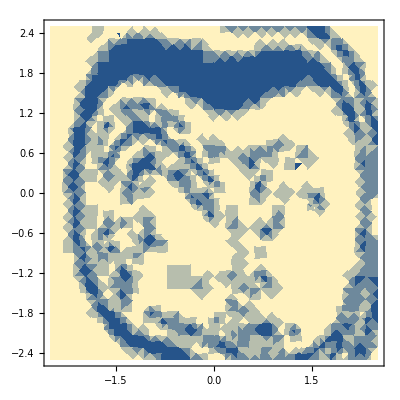

```mathematica
DensityPlot[frac[0.1,4π,a,b,0.25,1,0.25],{a,-2.5,2.5},{b,-2.5,2.5} ,PlotPoints-> 130,MaxRecursion-> 3]
```